Import::nffil: File not found during Import.

Part::partw: Part 3 of Transpose[$Failed] does not exist.

Part::partw: Part 4 of Transpose[$Failed] does not exist.

Part::partw: Part 9 of Transpose[$Failed] does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {Transpose[$Failed] ⟦ 3 ⟧, Transpose[$Failed] ⟦ 4 ⟧} cannot be transposed.

Part::partw: Part 3 of Transpose[$Failed] does not exist.

Part::partw: Part 4 of Transpose[$Failed] does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {Transpose[$Failed] ⟦ 3 ⟧, Transpose[$Failed] ⟦ 4 ⟧} cannot be transposed.

ListPlot::lpn: Transpose[{Transpose[$Failed] ⟦ 3 ⟧, Transpose[$Failed] ⟦ 4 ⟧}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

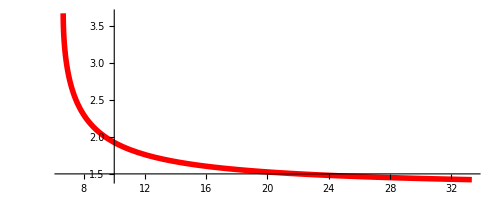
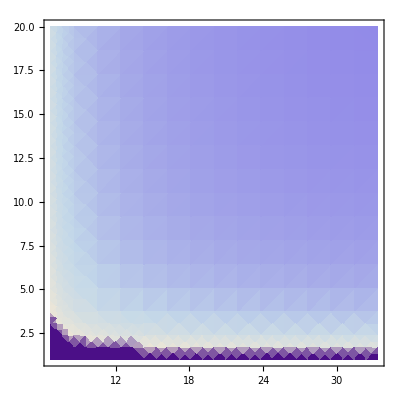
Show[-Graphics-,-Graphics-,ListPlot[Transpose[{Transpose[$Failed]⟦3⟧,Transpose[$Failed]⟦4⟧}],PlotStyle→{RGBColor[0,1,0],PointSize[0.01]}]]

Part::partw: Part 3 of Transpose[$Failed] does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {XD, YD, ZD} cannot be transposed.

ListPointPlot3D::arrayerr: {Transpose[{XD, YD, ZD}], {{cc, NN, If[1 + Re[Plus[« 2 »]] > 0. && Im[Times[« 3 »] + Power[« 2 »]] < 1/100000000, mna, 0.]}, {cc, NN, If[1 + Re[Plus[« 2 »]] > 0. && Im[Times[« 3 »] + Power[« 2 »]] < 1/100000000, mna, 0.]}}} must be a valid array or a list of valid arrays.

ListPointPlot3D[{Transpose[{XD,YD,ZD}],{{cc,NN,If[1+Re[-1/(cc (0.183333 (2-2 √(1-6.66667/cc)-6.66667/cc) cc-0.005 (8-8 √(1-6.66667/cc)-44.4444/cc^2-26.6667/cc) cc^2))+1/NN]>0.&&Im[-1/(cc (0.183333 (2-2 √(1-6.66667/cc)-6.66667/cc) cc-0.005 (8-8 √(1-6.66667/cc)-44.4444/cc^2-26.6667/cc) cc^2))+1/NN]<1/100000000,mna,0.]},{cc,NN,If[1+Re[-1/(cc (0.183333 (2-2 √(1-6.66667/cc)-6.66667/cc) cc-0.005 (8-8 √(1-6.66667/cc)-44.4444/cc^2-26.6667/cc) cc^2))+1/NN]>0.&&Im[-1/(cc (0.183333 (2-2 √(1-6.66667/cc)-6.66667/cc) cc-0.005 (8-8 √(1-6.66667/cc)-44.4444/cc^2-26.6667/cc) cc^2))+1/NN]<1/100000000,mna,0.]}}}]

```mathematica
a2[λ_]:=(1-√(1-12λ))/(6λ);
G[n_,λ_]:=((2n)!)/(n!(n+2)!)a2[λ]^n(2n+2 -n a2[λ]);
ξN[α_,λ_,nmax_]:=Sum[G[n,λ] α^(2n),{n,1,nmax}];
ξ[α_,λ_]:=1/(2 α^2)(1/2-λ a2[λ])(2-4 α^2 a2[λ]-2 √(1-4 α^2 a2[λ]))-λ/(16 α^4)(8-16 α^2 a2[λ]-16 α^4 a2[λ]^2-8 √(1-4 α^2 a2[λ]));
λ0=0.08;
cmin=4 a2[λ0];
cmax=5cmin;
GrA=ParametricPlot[{c,c ξ[1/(√c),λ0]},{c,cmin,cmax},PlotStyle->{RGBColor[1,0,0],Thickness[0.01]},PlotRange->All];
GrB=DensityPlot[If[NN>c ξ[1/(√c),λ0],1-1/(c ξ[1/(√c),λ0])+1/NN,0.0],{c,cmin,cmax},{NN,1.0,20.0},Mesh->False];
M=Import["G:\\LAT\\sd_metropolis\\data\\hmm\\mc_stat_mnatest_nmc20000000_l0.0800.dat"];
M=Transpose[M];
ccD=M[[3]];
NND=M[[4]];
mnaD=M[[9]];
GrC=ListPlot[Transpose[{ccD,NND}],PlotStyle->{RGBColor[0,1,0],PointSize[0.01]}];
Show[GrA,GrB,GrC]
MTP1=Table[
mna=1-1/(cc ξ[1/(√cc),λ0])+1/NN;
(*If[Re[mna]>0.0&&Abs[Im[mna]]<10^-8,
err=Abs[(mna-M[[9,i]])/mna];
Print["cc = ",cc,", NN = ",NN," <na> from simulations = ",M[[9,i]],", from formula = ",mna,", rel.err = ",Round[100.0err],"%"];
];*)
{cc,NN,If[Re[mna]>0.0&&Im[mna]<10^-8,mna,0.0]},
{i,1,Length[M[[3]]]}];
MTP=Transpose[{XD,YD,ZD}];
ListPointPlot3D[{MTP,MTP1}]
```

```mathematica
λ0=1/12;
cmin=4 a2[λ0];
cmax=6cmin;
GrA=ParametricPlot3D[{c,c ξ[1/(√c),λ0],1.0},{c,cmin,cmax},PlotStyle->{RGBColor[1,0,0],Thickness[0.01]},PlotRange->All];
GrB=Plot3D[If[NN>c ξ[1/(√c),λ0],1-1/(c ξ[1/(√c),λ0])+1/NN,0.0],{c,cmin,cmax},{NN,1.0,40.0},Mesh->False];
Show[GrB,GrA]
```

-Graphics3D-

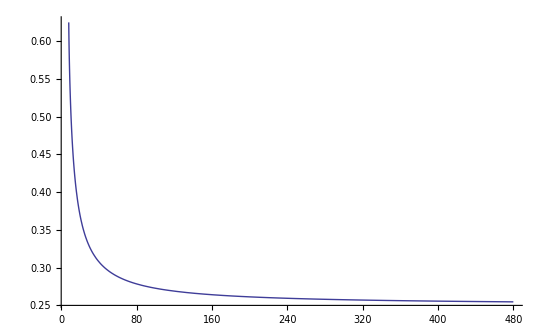

```mathematica
Plot[1-1/(c ξ[1/(√c),λ0]),{c,cmin,60cmin},PlotRange->All]
```

```mathematica
N[FullSimplify[Limit[1/(c ξ[1/(√c),0.1/12]),{c->+∞}]]]
```

{0.98297}

```mathematica
a2[λ_]:=(1-√(1-12λ))/(6λ);
F0[λ_]:=1/2 Log[a2[λ]]-1/24(1-a2[λ])(9-a2[λ]);
FullSimplify[D[F0[λ],λ]]
```

-((-1+√(1-12 λ)+6 λ) (-1+√(1-12 λ)+3 λ (7-5 √(1-12 λ)+36 λ)))/(216 λ^3 (-1+√(1-12 λ)+12 λ))

```mathematica
D[a2[λ],λ]
```

-(1-√(1-12 λ))/(6 λ^2)+1/(√(1-12 λ) λ)

```mathematica
n=6;cnt=0;
For[n1=1,n1≤n,n1++,
For[n2=1,n2≤n,n2++,
If[n1+n2==n,cnt++]
];
];
cnt
```

5

```mathematica
M=Import["G:\\LAT\\sd_metropolis\\data\\gw_sc\\mc_stat_l3.0000_nmc50000000.dat"];
M=Transpose[M];
Print[MatrixForm[M]];
ccD=M[[3]];
NND=M[[4]];
mnaD=M[[9]];
(*ssaD=M[[13]];*)
accD=M[[7]];
DTP=Transpose[{ccD,NND,mnaD}];
GrA=ListPointPlot3D[DTP];
GrB=ListPlot3D[DTP,Mesh->False,PlotRange->All];
Show[GrA,GrB]
```

(3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
15. | 15. | 15. | 15. | 15. | 15. | 15. | 15. | 15. | 15. | 16. | 16. | 16. | 16. | 16. | 16. | 16. | 16. | 16. | 16. | 17. | 17. | 17. | 17. | 17. | 17. | 17. | 17. | 17. | 17. | 18. | 18. | 18. | 18. | 18. | 18. | 18. | 18. | 18. | 18. | 19. | 19. | 19. | 19. | 19. | 19. | 19. | 19. | 19. | 19. | 20. | 20. | 20. | 20. | 20. | 20. | 20. | 20. | 20. | 20. | 21. | 21. | 21. | 21. | 21. | 21. | 21. | 21. | 21. | 21. | 22. | 22. | 22. | 22. | 22. | 22. | 22. | 22. | 22. | 22. | 23. | 23. | 23. | 23. | 23. | 23. | 23. | 23. | 23. | 23. | 24. | 24. | 24. | 24. | 24. | 24. | 24. | 24. | 24. | 24. | 25. | 25. | 25. | 25. | 25. | 25. | 25. | 25. | 25. | 25. | 26. | 26. | 26. | 26. | 26. | 26. | 26. | 26. | 26. | 26. | 27. | 27. | 27. | 27. | 27. | 27. | 27. | 27. | 27. | 27. | 28. | 28. | 28. | 28. | 28. | 28. | 28. | 28. | 28. | 28. | 29. | 29. | 29. | 29. | 29. | 29. | 29. | 29. | 29. | 29. | 30. | 30. | 30. | 30. | 30. | 30. | 30. | 30. | 30. | 30.
2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8 | 2. | 2.2 | 2.4 | 2.6 | 2.8 | 3. | 3.2 | 3.4 | 3.6 | 3.8
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0.32132 | 0.32178 | 0.32119 | 0.16339 | 0.32415 | 0.33285 | 0.33996 | 0.3204 | 0.24798 | 0.53478 | 0.30184 | 0.30649 | 0.30215 | 0.30329 | 0.26275 | 0.3071 | 0.30386 | 0.30372 | 0.29111 | 0.39362 | 0.28539 | 0.28227 | 0.13626 | 0.14176 | 0.41948 | 0.28573 | 0.22177 | 0.32643 | 0.13425 | 0.29683 | 0.14038 | 0.13012 | 0.2731 | 0.12765 | 0.27153 | 0.1282 | 0.27608 | 0.50637 | 0.45763 | 0.47557 | 0.13042 | 0.26409 | 0.12979 | 0.4102 | 0.097773 | 0.29003 | 0.42453 | 0.58382 | 0.21267 | 0.11894 | 0.51829 | 0.50435 | 0.24514 | 0.11551 | 0.15324 | 0.50459 | 0.25397 | 0.16922 | 0.64028 | 0.64355 | 0.23102 | 0.12296 | 0.6022 | 0.15396 | 0.48326 | 0.066855 | 0.38869 | 0.59764 | 0.19201 | 0.28859 | 0.19719 | 0.23207 | 0.52404 | 0.37748 | 0.087241 | 0.60644 | 0.47294 | 0.30107 | 0.43546 | 0.42543 | 0.46489 | 0.10453 | 0.11144 | 0.10688 | 0.368 | 0.62189 | 0.46056 | 0.6173 | 0.57933 | 0.54392 | 0.57631 | 0.32084 | 0.37431 | 0.031203 | 0.030383 | 0.21121 | 0.20536 | 0.46091 | 0.19711 | 0.573 | 0.10174 | 0.50106 | 0.5075 | 0.10229 | 0.097644 | 0.19637 | 0.32656 | 0.56893 | 0.64314 | 0.62764 | 0.64507 | 0.03676 | 0.10832 | 0.18193 | 0.18765 | 0.53794 | 0.64511 | 0.090432 | 0.090506 | 0.036109 | 0.42681 | 0.47564 | 0.3199 | 0.057479 | 0.19201 | 0.19299 | 0.57178 | 0.57734 | 0.20073 | 0.64735 | 0.094109 | 0.60651 | 0.1716 | 0.18813 | 0.052786 | 0.029268 | 0.50881 | 0.4927 | 0.54133 | 0.57127 | 0.52298 | 0.41326 | 0.44669 | 0.40731 | 0.19869 | 0.57101 | 0.25505 | 0.6306 | 0.18233 | 0.66733 | 0.43116 | 0.16328 | 0.56005 | 0.1719 | 0.055332 | 0.54565 | 0.63814 | 0.63956 | 0.085481 | 0.28059
358.68 | 494.84 | 328.46 | 83.825 | 232.36 | 16.561 | 13.72 | 295.04 | 29.317 | 6.5243 | 567.99 | 227.74 | 336.13 | 89.594 | 24.751 | 13.346 | 226.1 | 146.12 | 128.18 | 12.878 | 330.2 | 354.92 | 161.6 | 129.86 | 10.068 | 288.62 | 22.63 | 18.745 | 88.048 | 17.803 | 61.187 | 97.235 | 113.23 | 69.284 | 134.13 | 78.747 | 179.41 | 6.572 | 8.1974 | 7.2191 | 129.51 | 106.7 | 54.882 | 8.1711 | 49.829 | 17.907 | 6.6663 | 4.2107 | 27.453 | 69.544 | 7.7995 | 6.5149 | 50.71 | 38.577 | 36.634 | 5.2425 | 56.187 | 34.168 | 3.4115 | 3.0382 | 181.67 | 21.963 | 3.9641 | 31.954 | 7.1997 | 25.281 | 9.9742 | 3.6474 | 17.62 | 17.676 | 26.143 | 112.81 | 6.8589 | 9.3906 | 37.194 | 4.1097 | 4.5903 | 14.247 | 8.0419 | 8.8099 | 6.5105 | 82.742 | 65.075 | 62.365 | 10.747 | 3.6171 | 6.0737 | 4.5014 | 4.3041 | 4.4996 | 4.8838 | 13.714 | 10.028 | 32.174 | 18.857 | 25.495 | 98.616 | 10.46 | 14.367 | 5.5334 | 56.545 | 4.627 | 4.829 | 100.26 | 42.445 | 65.853 | 7.7387 | 5.2773 | 3.5365 | 3.4342 | 3.7446 | 10.226 | 25.205 | 92.642 | 31.257 | 5.0995 | 3.0661 | 39.973 | 28.406 | 12.055 | 5.8014 | 11.765 | 11.727 | 11.577 | 66.944 | 36.255 | 4.0013 | 3.0618 | 9.0097 | 3.2109 | 40.692 | 4.3943 | 28.021 | 71.792 | 21.694 | 17.792 | 4.8318 | 5.6738 | 4.3275 | 3.0833 | 3.7269 | 6.5527 | 8.8351 | 5.9153 | 11.339 | 3.3816 | 8.7201 | 3.1185 | 51.519 | 2.9193 | 7.7159 | 23.055 | 5.0904 | 26.1 | 42.409 | 5.1817 | 2.8966 | 3.36 | 41.916 | 11.2
0.99148 | 0.98928 | 0.99182 | 0.94501 | 0.97994 | 0.70547 | 0.69392 | 0.9918 | 0.81419 | 0.50584 | 0.99853 | 0.98358 | 0.99658 | 0.99382 | 0.78938 | 0.72465 | 0.99161 | 0.99164 | 0.9278 | 0.63418 | 0.99921 | 0.97842 | 0.96817 | 0.9522 | 0.60217 | 0.99633 | 0.83352 | 0.70356 | 0.95904 | 0.72442 | 0.95903 | 0.97337 | 0.99114 | 0.97327 | 0.99486 | 0.96531 | 0.98042 | 0.52093 | 0.561 | 0.54175 | 0.96913 | 0.99158 | 0.95706 | 0.61736 | 0.94733 | 0.73178 | 0.58863 | 0.42596 | 0.81175 | 0.97317 | 0.50612 | 0.51492 | 0.93365 | 0.91731 | 0.91698 | 0.40413 | 0.98288 | 0.89073 | 0.36833 | 0.36161 | 0.98541 | 0.90942 | 0.41226 | 0.9127 | 0.53693 | 0.86149 | 0.6224 | 0.40647 | 0.81845 | 0.73338 | 0.82913 | 0.98749 | 0.48891 | 0.65282 | 0.83404 | 0.39637 | 0.43396 | 0.71617 | 0.57908 | 0.47453 | 0.55176 | 0.98147 | 0.9579 | 0.96654 | 0.65686 | 0.3818 | 0.55057 | 0.39314 | 0.42035 | 0.35524 | 0.43038 | 0.68472 | 0.64247 | 7.2729 | 7.274 | 0.81256 | 0.87098 | 0.55088 | 0.81743 | 0.4373 | 0.97297 | 0.40056 | 0.49919 | 0.96376 | 0.97268 | 0.97164 | 0.58485 | 0.43468 | 0.35747 | 0.37672 | 0.36508 | 7.8565 | 0.94951 | 0.95713 | 0.83283 | 0.47104 | 0.35744 | 0.98073 | 0.97605 | 7.8547 | 0.47865 | 0.5243 | 0.68232 | 0.84699 | 0.99843 | 0.81579 | 0.42563 | 0.3233 | 0.59858 | 0.35182 | 0.97178 | 0.40712 | 0.82604 | 0.98644 | 0.85872 | 8.4712 | 0.4854 | 0.50089 | 0.45859 | 0.33171 | 0.37198 | 0.4922 | 0.56759 | 0.49092 | 0.80894 | 0.33386 | 0.64016 | 0.36913 | 0.99023 | 0.31881 | 0.5704 | 0.73515 | 0.4616 | 0.9239 | 0.84826 | 0.45337 | 0.35823 | 0.36139 | 0.96236 | 0.73661
0.00027525 | 0.00027537 | 0.00027611 | 0.00027107 | 0.00027539 | 0.00023979 | 0.0002384 | 0.0002776 | 0.00025635 | 0.00020679 | 0.00028756 | 0.00028614 | 0.00028795 | 0.00028802 | 0.00026152 | 0.00025199 | 0.00028855 | 0.00028887 | 0.00028137 | 0.00023854 | 0.00029855 | 0.00029639 | 0.00029558 | 0.00029357 | 0.00023957 | 0.00029968 | 0.00027816 | 0.00025818 | 0.00029581 | 0.00026215 | 0.000304 | 0.0003063 | 0.00030894 | 0.00030694 | 0.00030988 | 0.00030639 | 0.00030854 | 0.00023162 | 0.00024028 | 0.00023658 | 0.0003157 | 0.00031896 | 0.00031429 | 0.00025791 | 0.00031332 | 0.00027961 | 0.00025288 | 0.00021638 | 0.00029381 | 0.00031814 | 0.0002401 | 0.00024238 | 0.00032059 | 0.00031896 | 0.00031845 | 0.00021618 | 0.00032882 | 0.00031545 | 0.00020693 | 0.00020531 | 0.00033773 | 0.00032557 | 0.00022327 | 0.00032717 | 0.00025545 | 0.00031965 | 0.00027478 | 0.00022318 | 0.00031294 | 0.00029741 | 0.00032086 | 0.00034738 | 0.00024976 | 0.00028773 | 0.00032331 | 0.00022562 | 0.0002364 | 0.00030191 | 0.00027264 | 0.00024825 | 0.00027132 | 0.00035565 | 0.00035208 | 0.00035375 | 0.00029584 | 0.000227 | 0.00027268 | 0.00023104 | 0.00023887 | 0.00021959 | 0.00024565 | 0.00030861 | 0.00029952 | 0.00032875 | 0.00032847 | 0.00033549 | 0.00034673 | 0.00027968 | 0.00033656 | 0.00024989 | 0.00037193 | 0.00024262 | 0.00027084 | 0.00037064 | 0.00037234 | 0.00037264 | 0.00029451 | 0.00025416 | 0.00023057 | 0.00023675 | 0.00023613 | 0.00036019 | 0.00037648 | 0.00037753 | 0.00035481 | 0.00026994 | 0.00023504 | 0.00038256 | 0.00038242 | 0.00036011 | 0.00027671 | 0.00028952 | 0.00033038 | 0.00036524 | 0.00039398 | 0.00035949 | 0.00026225 | 0.00022793 | 0.0003105 | 0.00023877 | 0.00039598 | 0.00026051 | 0.00036826 | 0.00039988 | 0.00037601 | 0.00038509 | 0.00028572 | 0.00029032 | 0.00027747 | 0.00023618 | 0.00025331 | 0.00029195 | 0.00031346 | 0.0002919 | 0.0003731 | 0.00024068 | 0.00033332 | 0.000254 | 0.00040941 | 0.000236 | 0.0003192 | 0.00036214 | 0.00028841 | 0.00040308 | 0.00038819 | 0.00028673 | 0.0002547 | 0.00025609 | 0.00041138 | 0.0003638
7.0333 | 7.2323 | 7.4315 | 7.6308 | 7.8302 | 8.0296 | 8.2292 | 8.4288 | 8.6284 | 8.8281 | 7.3646 | 7.5636 | 7.7628 | 7.9622 | 8.1616 | 8.3611 | 8.5607 | 8.7603 | 8.96 | 9.1596 | 7.6961 | 7.8952 | 8.0944 | 8.2938 | 8.4933 | 8.6928 | 8.8924 | 9.092 | 9.2917 | 9.4914 | 8.0278 | 8.2269 | 8.4262 | 8.6256 | 8.8251 | 9.0247 | 9.2243 | 9.424 | 9.6237 | 9.8234 | 8.3596 | 8.5589 | 8.7582 | 8.9576 | 9.1571 | 9.3567 | 9.5564 | 9.756 | 9.9558 | 10.155 | 8.6917 | 8.8909 | 9.0903 | 9.2897 | 9.4893 | 9.6889 | 9.8885 | 10.088 | 10.288 | 10.488 | 9.0238 | 9.2231 | 9.4225 | 9.622 | 9.8215 | 10.021 | 10.221 | 10.421 | 10.62 | 10.82 | 9.3561 | 9.5554 | 9.7548 | 9.9543 | 10.154 | 10.354 | 10.553 | 10.753 | 10.953 | 11.152 | 9.6884 | 9.8877 | 10.087 | 10.287 | 10.486 | 10.686 | 10.886 | 11.085 | 11.285 | 11.485 | 10.021 | 10.22 | 10.42 | 10.619 | 10.819 | 11.019 | 11.218 | 11.418 | 11.618 | 11.818 | 10.353 | 10.553 | 10.752 | 10.952 | 11.151 | 11.351 | 11.551 | 11.751 | 11.95 | 12.15 | 10.686 | 10.885 | 11.085 | 11.284 | 11.484 | 11.684 | 11.883 | 12.083 | 12.283 | 12.483 | 11.019 | 11.218 | 11.417 | 11.617 | 11.817 | 12.016 | 12.216 | 12.416 | 12.616 | 12.816 | 11.351 | 11.551 | 11.75 | 11.95 | 12.149 | 12.349 | 12.549 | 12.749 | 12.949 | 13.148 | 11.684 | 11.883 | 12.083 | 12.283 | 12.482 | 12.682 | 12.882 | 13.082 | 13.281 | 13.481 | 12.017 | 12.216 | 12.416 | 12.615 | 12.815 | 13.015 | 13.215 | 13.414 | 13.614 | 13.814
0.83402 | 0.83402 | 0.83402 | 0.2524 | 0.83402 | 0.028891 | 0.028654 | 0.83402 | 0.2524 | 0.027367 | 0.83951 | 0.83951 | 0.83951 | 0.83951 | 0.20302 | 0.026825 | 0.83951 | 0.83951 | 0.77778 | 0.068587 | 0.83951 | 0.80247 | 0.2524 | 0.2524 | 0.025606 | 0.83951 | 0.2524 | 0.024928 | 0.2524 | 0.024387 | 0.2524 | 0.2524 | 0.83951 | 0.2524 | 0.83951 | 0.2524 | 0.83951 | 0.023438 | 0.042676 | 0.023099 | 0.2524 | 0.8642 | 0.2524 | 0.042676 | 0.056089 | 0.19204 | 0.022558 | 0.022405 | 0.022558 | 0.2524 | 0.024387 | 0.023709 | 0.8642 | 0.034141 | 0.2524 | 0.021795 | 0.8642 | 0.2524 | 0.020576 | 0.020576 | 0.80247 | 0.034141 | 0.022558 | 0.2524 | 0.021338 | 0.020576 | 0.020119 | 0.020576 | 0.020576 | 0.019712 | 0.022558 | 0.8642 | 0.021338 | 0.020661 | 0.020576 | 0.019662 | 0.019662 | 0.019052 | 0.042676 | 0.019052 | 0.021338 | 0.2524 | 0.2524 | 0.2524 | 0.019441 | 0.019052 | 0.0189 | 0.018747 | 0.017833 | 0.017833 | 0.020576 | 0.019662 | 0.019441 | 0. | 0. | 0.2524 | 0.88889 | 0.017833 | 0.01768 | 0.017833 | 0.2524 | 0.019052 | 0.018493 | 0.2524 | 0.2524 | 0.80247 | 0.017833 | 0.017375 | 0.016461 | 0.016461 | 0.019052 | 0. | 0.20302 | 0.75309 | 0.88889 | 0.017071 | 0.016461 | 0.2524 | 0.2524 | 0. | 0.017833 | 0.017833 | 0.017375 | 0.016461 | 0.88889 | 0.53086 | 0.016461 | 0.015546 | 0.75309 | 0.015546 | 0.2524 | 0.016918 | 0.88889 | 0.88889 | 0.016461 | 0. | 0.015546 | 0.015208 | 0.014937 | 0.014937 | 0.016461 | 0.016461 | 0.016122 | 0.015546 | 0.015546 | 0.014937 | 0.014937 | 0.014632 | 0.88889 | 0.014293 | 0.016461 | 0.8642 | 0.015445 | 0.88889 | 0.014937 | 0.014632 | 0.014632 | 0.014022 | 0.2524 | 0.013955)

-Graphics3D-

```mathematica
D
```

```mathematica
λ0=0.08;
cmin=4 a2[λ0];
N[cmin]
N[cmin ξ[1/(√cmin),λ0]]
```

3.7037-6.62274×10^-8 ⅈ

```mathematica
λ0=1/12;
cmin=4 a2[λ0]
N[cmin ξ[1/(√cmin),λ0]]
```

8

2.66667